```mathematica
(*Mathematica*)
```

```mathematica
ph[z_]=(z^2-8 z^4+28 z^6-56 z^8+70 z^10-56 z^12+28 z^14-8 z^16+z^18)/((1+z^2)^4 (1-6 z^2+z^4)^2)
```

(z^2-8 z^4+28 z^6-56 z^8+70 z^10-56 z^12+28 z^14-8 z^16+z^18)/((1+z^2)^4 (1-6 z^2+z^4)^2)

```mathematica
w=x/.NSolve[ph[x]==0,x]//Chop
```

{1.,1.-6.15285×10^-18 ⅈ,1.+6.15285×10^-18 ⅈ,-1.-4.20986×10^-20 ⅈ,-1.+4.20986×10^-20 ⅈ,-1.-1.01635×10^-19 ⅈ,-1.+1.01635×10^-19 ⅈ,1.-8.70144×10^-18 ⅈ,1.+8.70144×10^-18 ⅈ,-1.-1.01635×10^-19 ⅈ,-1.+1.01635×10^-19 ⅈ,-1.-4.20986×10^-20 ⅈ,-1.+4.20986×10^-20 ⅈ,1.-6.15285×10^-18 ⅈ,1.+6.15285×10^-18 ⅈ,1.,0.,0.}

```mathematica
max=Max[Norm/@w]+1
```

2.

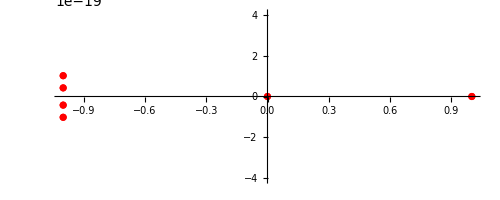

```mathematica
ComplexListPlot[w,PlotStyle->Red,ImageSize->Full]
```

```mathematica
ga=ComplexPlot3D[ph[z],{z,-max-max*I,max+max*I},ColorFunction->"CyclicReImLogAbs",ImageSize->4000];
```

```mathematica
Export["j_1000_hermanrings_Spontaneous_Magnetization_function_ComplexPlot_ga.jpg",ga]
```

j_1000_hermanrings_Spontaneous_Magnetization_function_ComplexPlot_ga.jpg

```mathematica
Clear[g1,g2]
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Oct 2026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=ph[nz];
        ++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-2.5+0.0001,2.5,1000},{-2.5+0.001,2.5,1000}}];
```

General::munfl: (-9.72307×10^-22+2.15756×10^-19 ⅈ)^18 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→Hue,Background→Black,ViewPoint→Above,ImageSize->2*{2000,2000}];
```

```mathematica
Export["j_1000_hermanrings_2Spontaneous_Magnetization_function_In_Out_monitor_g1.jpg",g1]
```

j_1000_hermanrings_Spontaneous_Magnetization_function_In_Out_monitor_g1.jpg

j_1000_hermanrings_2Spontaneous_Magnetization_function_In_Out_monitor_g1.jpg

```mathematica
arraym=FractalPureM[{{-2.5+0.0001,2.5,2000},{-2.5+0.001,2.5,2000}}];
```

General::munfl: (-8.89984×10^-21+4.34927×10^-19 ⅈ)^18 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.89912×10^-19-3.39677×10^-18 ⅈ)^18 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.83715×10^-20-1.76913×10^-18 ⅈ)^18 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.81592×10^-21+4.51675×10^-19 ⅈ)^18 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-9.72307×10^-22+2.15756×10^-19 ⅈ)^18 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
g2=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction->Hue,ImageSize->2*{2000,2000},Frame->False];
```

```mathematica
Export["j_2000_hermanrings_Spontaneous_Magnetization_function_In_Out_monitor_g2.jpg",g2]
```

j_2000_hermanrings_Spontaneous_Magnetization_function_In_Out_monitor_g2.jpg

```mathematica
colortab=Reverse[Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2*{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_hermanrings_2Spontaneous_Magnetization_function_In_Out_monitor_g3.jpg",g3]
```

j_2000_hermanrings_Spontaneous_Magnetization_function_In_Out_monitor_g3.jpg

```mathematica
Export["j_2000_hermanrings_2Spontaneous_Magnetization_function_In_Out_monitor_grid.jpg",GraphicsGrid[{{ga,g2}, 
 {g3,g1}},ImageSize->8000]]
```

j_2000_hermanrings_Spontaneous_Magnetization_function_In_Out_monitor_grid.jpg

```mathematica
(*end*)
```